### R0<1: 6 important cases

crit vac=-((γ_r+Λ) (-β+γ+Λ+ν_i))/(-β_r+γ+Λ+ν_i)crit vac when br=0 -((γ_r+Λ) (-β+γ+Λ+ν_i))/(γ+Λ+ν_i)

crit β=β_r+((γ_r+γ_s+Λ) (-β_r+γ+Λ+ν_i))/(γ_r+Λ)

Null^2

Immunity isos (β-β_r)+β_r-γ-Λ-ν_i+i (-β_r+ν_i)

D = {(β+γ_s+Λ-ν_i-√((β+γ_s+Λ-ν_i)^2+4 Λ (-β+ν_i)))/(2 (β-ν_i)),-(-β+γ_s+Λ+ν_i-√((β+γ_s+Λ-ν_i)^2+4 Λ (-β+ν_i)))/(2 (β-ν_i))}

E= {0,(γ_r+Λ)/γ_r}

A = {-(-γ-Λ)/(β-ν_i),-(-β+γ+Λ+ν_i)/(β-ν_i)}

B= {(-β_r+γ+Λ+ν_i)/(β-β_r),0}

C= {0,(-β_r+γ+Λ+ν_i)/(-β_r+ν_i)}

new case: 0<β_r<γ+Λ+ν_i&&β>γ+Λ+ν_i&&γ_r>0&&γ_s>-((γ_r+Λ) (-β+γ+Λ+ν_i))/(-β_r+γ+Λ+ν_i)

Discrim= 4 (β-β_r) (γ γ_r+Λ (β_r+γ_r-ν_i)) (β-ν_i)+(β_r (γ_s+Λ)+β (β_r-γ+γ_r-Λ-ν_i)-(β_r-γ+γ_r+γ_s) ν_i+ν_i^2)^2

(γ (β-ν_i) (β+2 γ_r+Λ-ν_i)+2 √(γ (γ_r+Λ) (β-ν_i)^2 (β+γ_r-ν_i) (-β+γ+Λ+ν_i))-(β-Λ-ν_i) (β (γ_r+Λ)-(β+γ_r) ν_i+ν_i^2))/(-β+Λ+ν_i)^2

β^2+γ_s^2+2 β (γ_s-Λ-ν_i)+2 γ_s (Λ-ν_i)+(Λ+ν_i)^2

J at DFE =(-γ_r-γ_s-Λ | -γ_r-(β (γ_r+Λ))/(γ_r+γ_s+Λ)+((γ_r+Λ) ν_i)/(γ_r+γ_s+Λ)
0 | -γ-Λ+(β (γ_r+Λ))/(γ_r+γ_s+Λ)+β_r (1-(γ_r+Λ)/(γ_r+γ_s+Λ))-ν_i)

cases, β>Lgn, γs>gsc, wh: {{1,True,True,1},{2,False,False,4},{3,False,False,4},{4,False,False,4},{5,False,True,6},{6,False,True,6}}

R0, γs > cr vac, sign of the slope: {{1,0.952381,True,1,True,1,True},{2,0.53125,False,4,False,-1,True},{3,0.769231,False,4,True,-1,False},{4,0.907372,False,4,True,-1,True},{5,0.633333,True,6,True,1,True},{6,0.0925926,True,6,False,-1,True}}

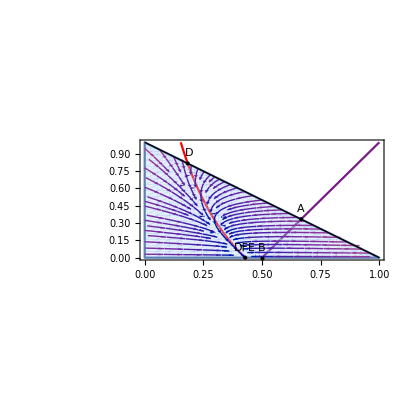
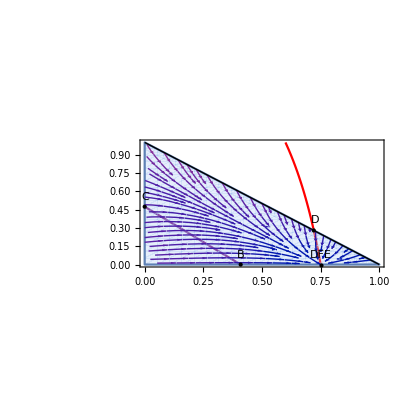
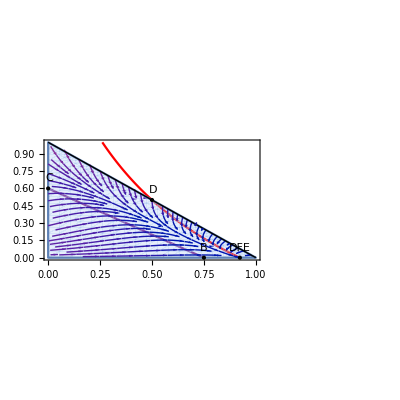
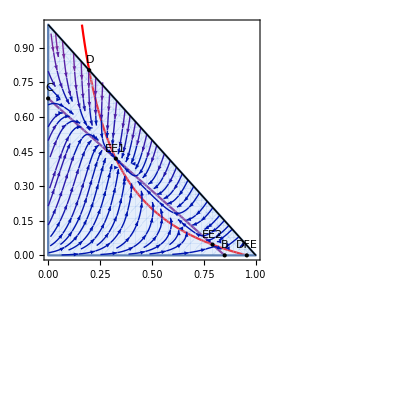
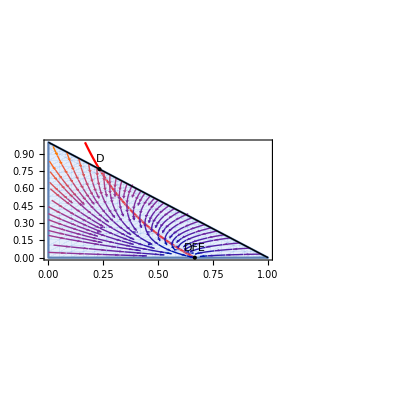
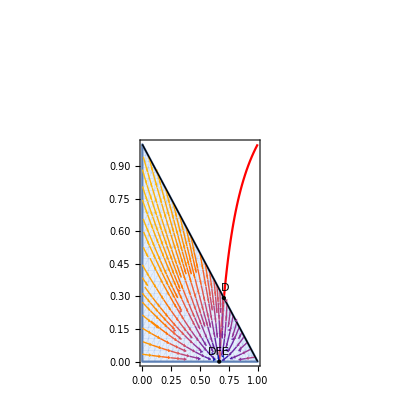

```mathematica
SetDirectory[NotebookDirectory[]];
AppendTo[$Path,Directory];
Clear["Global`*"];
Format[γs]:=Subscript[γ,s];
Format[γr]:=Subscript[γ,r];
Format[νr]:=Subscript[ν,r];
Format[νi]:=Subscript[ν,i];
Format[βr]:=Subscript[β,r];
j=1;
cp={β>0,βr>0,Λ>0,νi>0,γ>0,γr>0,γs>0}; 
νr= 0; sd=(Λ+γr)/(Λ+γr+γs);rd=1-sd;R0=(β sd+(βr+νr)rd)/(Λ+νi+γ);DFE={sd,0};Lgn=γ +  Λ +νi;cR=β>Lgn;cRr=βr >Lgn;
einD[p_]:=If[Element[p[[1]],Reals],Boole[p[[1]]>=0&&p[[2]]>=0&&p[[1]]+p[[2]]<=1],-1];
Print["crit vac=",gsc=γs/.Solve[(R0)==1,γs][[1]]//FullSimplify , "crit vac when br=0 ",gsc/.βr->0];(*critical vac*)
Print["crit β=",bz=βr+(Lgn-βr)/sd]
wh=Which[β>γ +  Λ +νi>βr,1,β>βr>γ +  Λ +νi,2,βr>β>γ +  Λ +νi,3,βr>γ +  Λ +νi>β,4,γ +  Λ +νi>βr>β,5,γ +  Λ +νi>β>βr,6];
cDerg=γs->0;
csc={z1->1, z->1};(*scaled*)
cr={z1->1, z->1,r->1-i-s};ci=i->1-s;
(******scaled   General case******)
ex=(νi i +   νr  r); si=po=0;
s1=Λ - β  s i^(po +1)+ γr r -(γs+Λ) s+ (z1 s) ex;
ifa=(β s  i^po+ βr r-(γ+νi +Λ )   +  z νi  i  +z1   νr r)  ;
i1=  i  (ifa) + si s;
r1=-βr r i+ γ i -(γr +Λ+νr) r + (γs -si) s +z1 (r  ex);

(*Fixed points*)
var={s,i};
vz={0,0};
ss=s1/.cr;
ii=i1/.cr;
Print["Immunity iso",iii=Collect[(ii/i),{s,i}]]
dynsc={ss,ii};
ifac=ifa/.cr;
sq=Collect[(νi-βr)ss/.i->(i/.Solve[ifac==0,i][[1]])//FullSimplify,s];
sqL=CoefficientList[sq,s];
Dis=sqL[[2]]^2-4 sqL[[1]] sqL[[3]]//FullSimplify;
ssi=ss/.ci;
sss=Collect[(ss/s),{s,i}];
Print["D = ",dD={sD,iD}={s,i}/.Solve[{sss==0,i==1-s},{s,i}][[1]]//FullSimplify]

iE=i/.Solve[(ss/.s->0)==0,{i}][[1]];
Print["E= ", eE={0,iE}]
iii=Collect[(ii/i),{s,i}];
Print["A = ",A={sA,iA}={s,i}/.(Solve[{(iii)==0,s+i==1},{s,i}][[1]])]
sB=s/.(Solve[(ifac/.i->0)==0,s][[1]]);
Print["B= ", B={sB,0}]
iC=i/.(Solve[(ifac/.s->0)==0,i][[1]]);
Print["C= ", cC={0,iC}]
(****Endemic Points****)
eqsc=Thread[{ss,ifac}==vz];
equsc=Solve[eqsc,var]//FullSimplify;
EE1={s/. equsc[[1]],i/. equsc[[1]]};
EE2={s/. equsc[[2]] ,i/. equsc[[2]]};
(*****Discriminant and its roots***)
Print["new case: ",Drop[Reduce[Join[{cR,1>sB>sd},cp],γs],3]//FullSimplify]
Print["Discrim= ",Dis//FullSimplify]
(*Solve[Dis==0,γs]//FullSimplify*)
cb=Solve[(Dis)==0,βr]//FullSimplify;
(*Print["Dis>0 ",Reduce[Join[{Discrim>0},cp],βr]]*)
brm=βr/.cb[[1]]//FullSimplify;
brp=βr/.cb[[2]]//FullSimplify;
brp/.cDerg//FullSimplify
dN=Denominator[brp]//FullSimplify
Length[bd=FullSimplify[brp dN]];
bdr=Apart[(bd-bd[[5]])/dN];
mL=(bd[[5]]/2)^2//FullSimplify;
(*******************R0<1*************************)

cD[1]={β->4,βr->2,Λ->1,νi->1,γ->1,γr->1/2,γs->2}(* βr<(γ+Λ+ νi )<β, νi<β*);
cD[2]={ β ->3/100,γ ->7/100 ,  Λ ->3/100,νi ->6/100,βr ->25/100,γs ->2/100 ,γr ->3/100   }(* (γ+Λ+ νi )<βr<β, νi>β*);
cD[3]={ β ->1/10,γ ->7/100 ,  Λ ->3/100,νi ->5/100,βr ->30/100,γs ->1/200 ,γr ->3/100  }(* νi<β<(γ+Λ+ νi )<βr*);
cD[4]={ β ->2/10,βr ->4/10,γ ->7/100 ,γr ->1/1000,  Λ ->1/100,νi ->15/100,  γs->1/2000}(*νi <β <(γ+Λ+ νi )<βr*);
cD[5]={β->4,βr->3/2,Λ->1,νi->1,γ->3,γr->1,γs->1}(*νi <βr<β <(γ+Λ+ νi )*);
cD[6]={β->1/2,βr->1/4,Λ->1,νi->2.5,γ->1,γr->1,γs->1}(*βr <β<νi <(γ+Λ+ νi )*);
nc=6;

Print["J at DFE =",jacDFE=Grad[dynsc,var]/.s->sd/.i->0;jacDFE//MatrixForm]
Print["cases, β>Lgn, γs>gsc, wh: ",   Table[{j,cR,γs>gsc,wh}//.cD[j],{j,nc}]]
(*Print["{brm,brp}=",{brm,brp}/.{β->1,βr->5/4,Λ->1/8,νi->1/2,γ->9/16,γr->1,γs->0}]
Print["{brm,brp}=",{brm,brp}//.cD[5]//N]*)
(*Print["Cases of Endemic points : ",Table[{j,equsc//.cD[j]//N},{j,nc}]]*)
fig[j_]:=Module[{epi,isos,isoi,sp},
epi={Text["EE1",Offset[{0,10},Re[{EE1[[1]],EE1[[2]]}  ]  //.cD[j]]],
{PointSize[Large],Style[Point[Re[{EE1[[1]],EE1[[2]]} ]  //.cD[j]],Blue]},Text["DFE",Offset[{0,10},
{DFE[[1]],DFE[[2]]}    //.cD[j]]],{PointSize[Large],Style[Point[{DFE[[1]],DFE[[2]]}    //.cD[j]],Black]},
Text["EE2",Offset[{0,10},Re[{EE2[[1]],EE2[[2]]}]    //.cD[j]]],{PointSize[Large],
Style[Point[Re[{EE2[[1]],EE2[[2]]} ]  //.cD[j]],Green]},Text["A",Offset[{0,10},{sA,iA}     //.cD[j]]],
{PointSize[Large],Style[Point[{sA,iA}   //.cD[j]],Purple]},Text["B",Offset[{0,10},B    //.cD[j]]],
{PointSize[Large],Style[Point[B    //.cD[j]],Yellow]},Text["D",Offset[{1,10},{sD,iD}   //.cD[j]]],
{PointSize[Large],Style[Point[{sD,iD}   //.cD[j]],Cyan]},
Text["C",Offset[{1,10},cC    //.cD[j]]],{PointSize[Large],Style[Point[cC    //.cD[j]],Brown]}
,Text["E",Offset[{0,10},eE   //.cD[j]]],{PointSize[Large],Style[Point[eE   //.cD[j]],Red]}};
isoi=ContourPlot[(iii    //.cD[j])==0,{s,0,1},{i,0,1},Epilog->epi,ColorFunction->"Rainbow"];
isos=ContourPlot[(ss    //.cD[j])==0,{s,0,1},{i,0,1},Epilog->epi,ColorFunction->Hue];
lin=Line[{{1,0},{0,1}}];
sp=StreamPlot[{dynsc  //.cD[j]},{s,0,1},{i,0,1},Epilog->epi,RegionFunction->Function[{s,i},i+s≤1],ImageSize->400,Frame->True,
 FrameLabel->{"s","i"},LabelStyle->Directive[Black,Medium]];
Show[{isoi,isos,sp,Graphics[lin]}]];
Print["R0, γs > cr vac, sign of the slope: ",Table[{j,R0//N,γs>gsc,wh,νi <β,Sign[(β-βr)/(βr-νi)],Dis>0}//.cD[j],{j,nc}]]
tb=Table[fig[j],{j,1,nc}]
```

### R0>1: 4 important cases

{{1,1.55556,True,2,True,1,True},{2,1.66869,True,3,True,-1,True},{3,1.20346,False,1,True,-1,True},{4,1.04762,True,4,True,-1,True}}

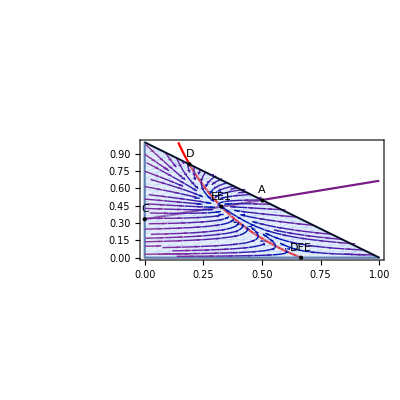
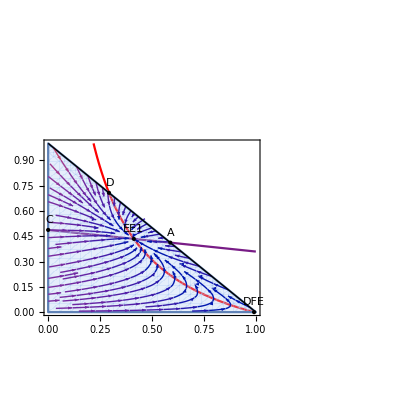
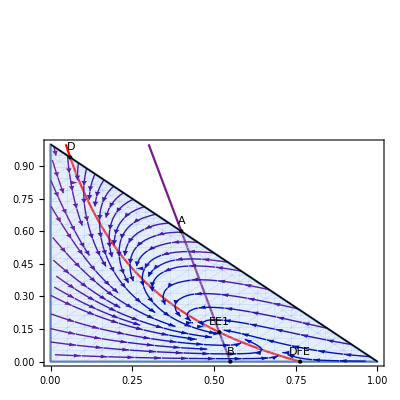
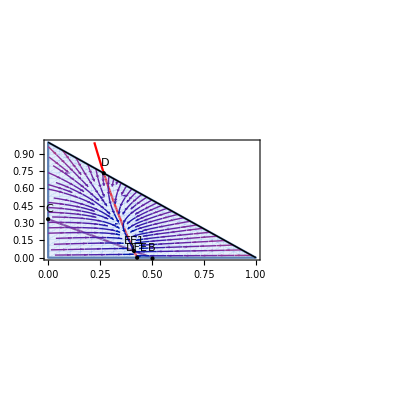

```mathematica
nc=4;
cD[1]={β->5,βr->4,(γ+Λ+ νi ) ->3,Λ->1,νi->1,γ->1,γr->1,γs->1};
(*βr>β >(γ+Λ+ νi )*)
(*βr>β >(γ+Λ+ νi )*)
cD[2]={β->7/2,βr->4,(γ+Λ+ νi ) ->21/10,Λ->1,νi->1/10,γ->1,γr->1/6,γs->1/100};
(*β >(γ+Λ+ νi )>βr, γs<γsc*)
cD[3]={ β ->30/100,βr ->1/10,(γ+Λ+ νi ) ->21/100 , γ ->5/100 ,  Λ ->1/100,νi ->15/100,   γs->15/1000, γr ->1/26      };
(*βr >(γ+Λ+ νi )>β, γs>γsc*)
cD[4]={β->2,βr->4,Λ->1,νi->1,γ->1,γr->1/2,γs->2};
Table[{j,R0//N,γs>gsc,wh,νi <β,Sign[(β-βr)/(βr-νi)],Dis>0}//.cD[j],{j,nc}]
tb=Table[fig[j],{j,1,nc}]
```

### Justifications

```mathematica
c4a=Reduce[Join[{1>sA>sD>0&& 1>sB>sd>0&& R0<1},cp],β]//FullSimplify
(*FindInstance[Join[{βr<Lgn<β&& νi <β&& R0<1&&einD[EE1]==1 },cp],{β,βr,Λ,νi,γ,γr,γs}]//FullSimplify*)
```

Λ>0&&γ_s>0&&γ>0&&ν_i>0&&0<β_r<γ+Λ+ν_i&&γ_r>0&&γ+Λ+ν_i<β<(-β_r γ_s+(γ_r+γ_s+Λ) (γ+Λ+ν_i))/(γ_r+Λ)

### Bifurcation Diagrams(This cell works after running the first one)

Dis[β]=0 : {{β→0.154592},{β→0.187931}}

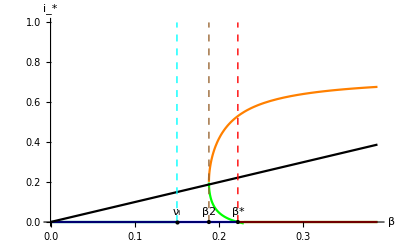

bif.pdf

```mathematica
cD={ βr ->4/10,γ ->7/100 ,γr ->1/1000,  Λ ->1/100,νi ->15/100,  γs->1/2000};
Print["Dis[β]=0 : " ,disb= Solve[(Dis)==0,β]//.cD//N//FullSimplify]
ee1=EE1[[2]]//.cD//N;
ee2=EE2[[2]]//.cD//N;
s1=EE1[[1]]//.cD;
ee2=EE2[[2]]//.cD//FullSimplify;s2=EE2[[1]]//.cD;
(*Print["βc, βc1, βc2", {bz//.cD//N,bc1=Re[β/.disb[[1]]//.cD]//N,bc2=Re[β/.disb[[2]]//.cD]//N}/.cD//N]*)
maxy=1;maxx=Max[β/.disb[[1]]//.cD,β/.disb[[2]]//.cD]+0.2;
p1=Plot[0,{β,0,bz//.cD},PlotStyle->{Blue,Thick}, AxesLabel->{"β","i_*"},PlotLegends->Style["DFE stable",Thick,Blue]];
p2=Plot[0,{β,bz//.cD,maxx},PlotStyle->{Red,Thick}, AxesLabel->{"β","i_*"},PlotLegends->Style["DFE unstable",Thick,Red]];
pt=Plot[β//.cD,{β,0,maxx},PlotStyle->{Black},PlotLegends->Style["i=β",Thick,Black]];

lic=Line[{{bz//.cD,0},{bz//.cD,maxy}}];
nu=Line[{{νi//.cD,0},{νi//.cD,maxy}}];
licp=Line[{{β/.disb[[2]]//.cD,0},{(β/.disb[[2]]//.cD),maxy}}];
litc=Graphics[{Thin,Red,Dashed,lic}];
linu= Graphics[{Thin,Cyan,Dashed,nu}];
litcp=Graphics[{Thin,Brown,Dashed,licp}];
p1t=Plot[ee1 Boole[s1>0&&s1+ee1<1],{β,0,maxx},PlotStyle->{Orange},PlotLegends->Style["EE1 stable sink",Thick,Orange], AxesLabel->{"β","i_*"}];
p2t=Plot[ee2  Boole[s2>0&&s2+ee2<1],{β,0,maxx},PlotStyle->{Green}, AxesLabel->{"β","i_*"},PlotLegends->Style["EE2 saddle point",Thick,Green]];
(*p2tu=Plot[ee2 //.cD,{β,0,maxx},PlotStyle->{Dashed,Blue}, AxesLabel->{"β","i_*"},PlotLegends->Style["EE2  unstable",Thick,Blue]];*)
(*pA=Plot[iA//.cD,{β,0,maxx},PlotStyle->{Cyan},PlotLegends->Style["iA",Cyan], AxesLabel->{"β","i_*"}];
pD=Plot[iD//.cD,{β,0,maxx},PlotStyle->{Green},PlotLegends->Style["iD",Thick,Green], AxesLabel->{"β","i_*"}];*)
bif=Show[{(*p2tu,*)p1t,p2t,p1,p2,pt,litc,litcp,linu},PlotRange->{{0,maxx},{0,1}},Epilog->{Text["β*",Offset[{0,10},{bz//.cD,0}]],{PointSize[Large],Style[Point[{bz//.cD,0}],Yellow]},
Text["ν_i",Offset[{0,10},{νi//.cD,0}]],{PointSize[Large],Style[Point[{νi//.cD,0}],Brown]},Text["β2",Offset[{0,10},{β/.disb[[2]]//.cD,0}]],{PointSize[Large],Style[Point[{β/.disb[[2]]//.cD,0}],Purple]}}]
Export["bif.pdf",bif]
```